## Large Parameter Distribution Benchmark

It was identified that a major source of slowdown is optimizing over parameters with wide distributions in grape. This benchmark will quantify the slowdown by comparing the running time of ``FindPulse`` as a function of the standard deviation of two parameters.

```mathematica
Needs["QuantumUtils`"];
```

## Parameter Distributions

```mathematica
uniformDistribution[parameter_, minimum_, maximum_, numberOfPoints_] := {
	ConstantArray[1/numberOfPoints, numberOfPoints], 
	Array[{(parameter -> #)}&, numberOfPoints, {minimum, maximum}]
}
```

## Single Distribution In Internal Hamiltonian

```mathematica
singleParameterInternalHamiltonianBenchmark[numberOfPoints_] := Module[
	{Hinternal, dist, controlRange, initialGuess, target, Hcontrol, tic, toc},
	Hinternal = 2π δω Spin[Z][1/2];
	dist = uniformDistribution[δω, -2, 2, numberOfPoints];
	controlRange = {{-1, 1}, {-1 , 1}};
	initialGuess:=FromPulse[Pulse[TimeSteps -> ConstantArray[0.1, 100], Pulse -> ConstantArray[{0, 0}, 100]]];
	target=MatrixExp[-I π Spin[X][1/2]/2];
	Hcontrol=2π{Spin[X][1/2],Spin[Y][1/2]};
	
	tic = AbsoluteTime[];
	FindPulse[initialGuess,target,0.99,controlRange,Hcontrol,Hinternal,ParameterDistribution->dist];
	toc = AbsoluteTime[];
	toc - tic
]
```

```mathematica
repeatBenchmark[repetitions_] := Function[{numberOfPoints}, Mean[Table[singleParameterInternalHamiltonianBenchmark[numberOfPoints], repetitions]]
];
```

```mathematica
times = Map[repeatBenchmark[10], Range[1, 6]];
```

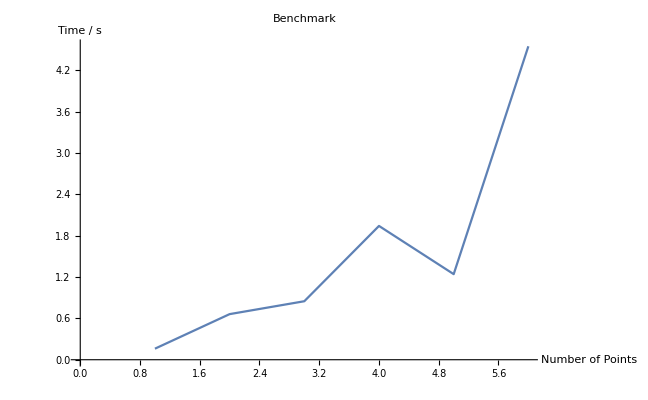

```mathematica
ListPlot[times, Joined->True, PlotLabel->"Benchmark", AxesLabel->{"Number of Points", "Time / s"}]
```

```mathematica
times
```

{0.03351,0.03484,0.034,0.135,0.043735,0.21856,0.24369,0.31799,0.3317,0.372954}

```mathematica
Hinternal = 2π δω Spin[Z][1/2];
dist = uniformDistribution[δω, -2, 2, 6];
controlRange = {{-1, 1}, {-1 , 1}};	initialGuess:=FromPulse[Pulse[TimeSteps -> ConstantArray[0.1, 100], Pulse -> ConstantArray[{0, 0}, 100]]];
target=MatrixExp[-I π Spin[X][1/2]/2];
Hcontrol=2π{Spin[X][1/2],Spin[Y][1/2]};
tic = AbsoluteTime[];
pulse = FindPulse[initialGuess,target,0.99,controlRange,Hcontrol,Hinternal,ParameterDistribution->dist, VerboseAscent-> True];
toc = AbsoluteTime[];
toc - tic
```

#rawUtilitypenaltyimprovementstepSizebestMultbetaResetCttoc (ms)

10.500.50.00240262.21

20.52322400.02322380.00440175.49

30.56928900.04606530.0056568520171.24

40.61430500.0450160.0056568510162.02

50.64503400.03072890.0056568510161.76

60.67460400.02957010.00820183.09

70.72998500.05538070.00810165.84

80.7651100.03512520.00810166.92

90.79683800.0317280.00810166.96

100.82513700.02829870.00810167.58

110.85009700.02496060.00810159.44

120.87190300.02180560.00810166.88

130.89079800.01889470.00810165.15

140.90705900.01626190.00810177.71

150.92097900.01391910.00810174.91

160.93284100.01186210.00810157.08

170.94291600.01007570.00810161.15

180.95145400.008537880.00810197.68

190.95867800.007223520.00810182.54

200.96478400.006106380.00810166.06

210.96994500.005160960.00810159.98

220.97430900.004363430.00810166.26

230.97800100.003692160.00810166.16

240.98112900.003127960.00810157.65

250.98378300.002654060.00810185.3

260.98603900.002256010.00810162.33

270.9879600.001921480.00810156.67

280.989600.001640020.00810183.47

290.99100300.001402860.00810180.43

5.263045

```mathematica
pulse
```

Head | Value
UtilityValue | 0.991003
PenaltyValue | 0
ExitMessage | Pulse of desired fidelity was found!
Target | (1/(√2) | -ⅈ/(√2)
-ⅈ/(√2) | 1/(√2))
InternalHamiltonian | (π δω | 0
0 | -π δω)
ControlHamiltonians | (0 | π
π | 0),(0 | -ⅈ π
ⅈ π | 0)
AmplitudeRange | {{-1,1},{-1,1}}
TimeSteps | {0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1}
Pulse | (0.121424 | 0.0313791 | -0.03304 | -0.0209892 | 0.0197876 | 0.0198446 | -0.015571 | -0.0235331 | 0.0148435 | 0.0365168 | -0.0181266 | -0.112623 | -0.14749 | -0.0831787 | 0.00911946 | 0.0373509 | -0.000350649 | -0.0281593 | -0.00389903 | 0.0274455 | 0.00918633 | -0.034072 | -0.0226787 | 0.06379 | 0.143582 | 0.128393 | 0.0352559 | -0.0349726 | -0.0239287 | 0.0205682 | 0.0226085 | -0.0156521 | -0.0266799 | 0.0138362 | 0.0410113 | -0.0117588 | -0.110779 | -0.151363 | -0.0876224 | 0.00873269 | 0.0397566 | 0.000507512 | -0.0299285 | -0.00514014 | 0.028954 | 0.0111671 | -0.0353032 | -0.0269515 | 0.0605575 | 0.144232 | 0.131188 | 0.0365646 | -0.0360226 | -0.0250511 | 0.0211087 | 0.0237161 | -0.0158707 | -0.0279434 | 0.0135878 | 0.0426714 | -0.00965184 | -0.109995 | -0.151798 | -0.087895 | 0.00917303 | 0.040154 | 0.000273609 | -0.0303051 | -0.00502033 | 0.0293075 | 0.0111292 | -0.035607 | -0.0269253 | 0.0607188 | 0.143529 | 0.129403 | 0.0350202 | -0.0360344 | -0.0240868 | 0.0213731 | 0.0229117 | -0.0162873 | -0.0270709 | 0.0143231 | 0.0413822 | -0.0121329 | -0.110459 | -0.148747 | -0.0839267 | 0.0103728 | 0.0384424 | -0.00103235 | -0.0291958 | -0.00352683 | 0.028429 | 0.00903359 | -0.0349509 | -0.0226084 | 0.064194 | 0.141487
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)
ParameterDistribution | {{1/6,1/6,1/6,1/6,1/6,1/6},{{δω→-2},{δω→-6/5},{δω→-2/5},{δω→2/5},{δω→6/5},{δω→2}}}
DistortionOperator | IdentityDistortion[]
PulsePenalty | ZeroPenalty[]